```mathematica
pressure[r_,r0_,τ_,E_]:=E τ r0 (r-r0)/r^3
```

```mathematica
pressureLaplace[r_,r0_,τ_,E_]:=(E τ)/r0(r/r0-1)
```

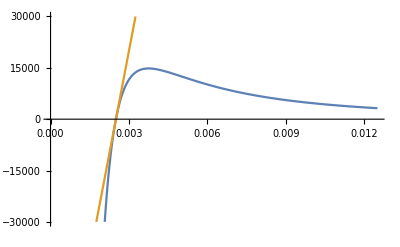

```mathematica
Plot[{
pressure[r,2.5 10^-3,0.5 10^-3,500000],
pressureLaplace[r,2.5 10^-3,0.5 10^-3,500000]
},{r,0,5 2.5 10^-3},PlotRange->{-30000,30000}]
```

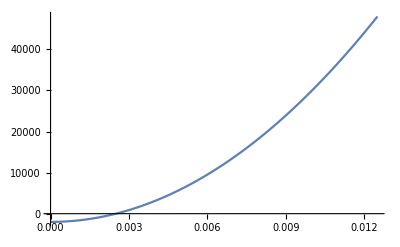

```mathematica
tubeLaw[r_,r0_,P0_,n_]:=P0((r/r0)^(2/n)-1)
Plot[tubeLaw[r,2.5 10^-3,2000,1],{r,0,5 2.5 10^-3}]
```

```mathematica
D[tubeLaw[r,r0,P0,n],r]//Simplify
%/.{r->r0}
D[pressure[r,r0,τ,Y],r]//Simplify
%/.{r->r0}
Solve[%%%==%,n]
```

(2 P0 (r/r0)^(2/n))/(n r)

(2 P0)/(n r0)

-((2 r-3 r0) r0 Y τ)/r^4

(Y τ)/r0^2

{{n→(2 P0 r0)/(Y τ)}}

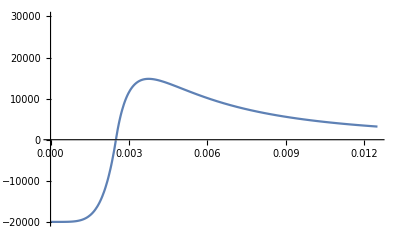

```mathematica
With[{r0=2.5 10^-3,τ=0.5 10^-3,E=500000,P0=20000},Plot[
If[r<r0,tubeLaw[r,r0,P0,(2 P0 r0)/(E τ)],pressure[r,r0,τ,E]]
,{r,0,5r0},PlotRange->{-20000,30000}]]
```

```mathematica
bucklingK[r_,r0_,p0_,k_,α_]:=p0+k(r/(α r0)-1)
bucklingK[r0,r0,p0,k,α]
D[bucklingK[r,r0,p0,k,α],r]
D[pressure[r,r0,τ,Y],r]/.{r->r0}
```

p0+k (-1+1/α)

k/(r0 α)

(Y τ)/r0^2

```mathematica
Solve[{k/(r0 α)==(Y τ)/r0^2,p0+k (-1+1/α)==0},{p0,k}]//Simplify
```

{{p0→(Y (-1+α) τ)/r0,k→(Y α τ)/r0}}

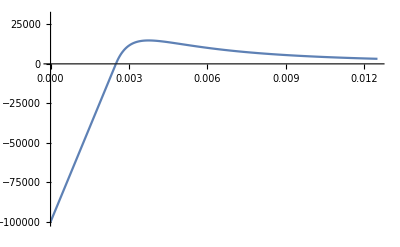

```mathematica
buckling[r_,r0_,τ_,Y_,α_]:=bucklingK[r,r0,(Y(-1+α) τ)/r0,(Y α τ)/r0,α]
With[{r0=2.5 10^-3,τ=0.5 10^-3,E=500000},Plot[
If[r<r0,buckling[r,r0,τ,E,0.6],pressure[r,r0,τ,E]]
,{r,0,5r0},PlotRange->{-100000,30000}]]
```